```mathematica
l[h_]:=√(h (1+h));
r[x_,h_]:=√(l[h]^2-x^2);
```

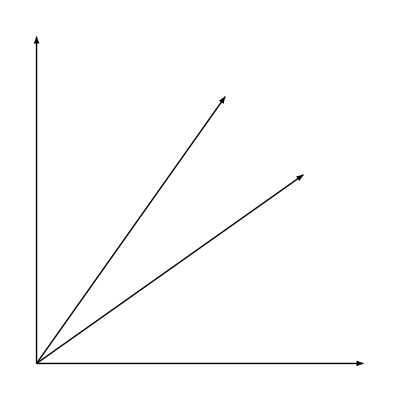

```mathematica
h=1/2;Graphics[{Arrow[{{0,0} ,{0,l[h]}}],Arrow[{{0,0} ,{h,r[h,h]}}],Arrow[{{0,0} ,{r[h,h],h}}],Arrow[{{0,0} ,{l[h],0}}]},AspectRatio->1]
```